# Математические основы защиты информации Лабораторная работа №5 Решетки

БГУ, ММФ, Каф. ДУиСА, 
 доцент Чергинец Д.Н.

## Введение

Пусть даны линейно независимые векторы v_1,v_2,...,v_m∈ℝ^n, m≤n. Множество векторов
L=L(v_1,v_2,...,v_m):={z_1 v_1+z_2 v_2+...+z_m v_m∈ℝ^n| z_1,z_2,...,z_m∈ℤ}
называется решеткой (lattice). Векторы v_1,v_2,...,v_m называются базисом решетки. У решетки как и у векторного пространства бесконечно много базисов. 

Векторы u_1,u_2,...,u_m∈ℝ^n являются базисом решетки L(v_1,v_2,...,v_m) тогда и только тогда, когда существует такая матрица M размерности m×m c целыми коэффициентами и det M=±1, что
U=M V,
где V  - матрица m×n, строками которой являются векторы v_1,v_2,..., v_m, а U - матрица со строками u_1,u_2,...,u_m.

Определителем решетки L(v_1,v_2,...,v_m) называется число
 d(L):=√(det(V V^T))=√(det(<v_1,v_1> | <v_1,v_2> | ... | <v_1,v_m>
<v_2,v_1> | <v_2,v_2> | ... | <v_2,v_m>
⋮ | ⋮ | … | ⋮
<v_m,v_1> | <v_m,v_2> | ... | <v_m,v_m>))
 Здесь < . , . > – скалярное произведение векторов.
 Определитель решетки является инвариантом, то есть не зависит от выбора базиса.

### Задание 1.

Изобразить решетку L(v_1,v_2) в окрестности начала координат. Элементы решетки изображать точками. Найти какой-нибудь другой базис решетки. Вычислить определитель решетки. Найти кратчайший ненулевой вектор решетки.

#### Вариант 4.

```mathematica
Subscript[v, 1]={6,3}
Subscript[v, 2]={1,3}
```

{6,3}

{1,3}

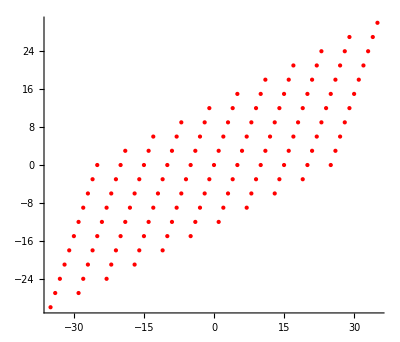

```mathematica
pnts = Table[i*Subscript[v, 1]+j*Subscript[v, 2],{i,-5,5},{j,-5,5}];
Graphics[{Red,Point[Flatten[pnts,1]]},Axes->True]
```

{{1,3},{4,-3}}

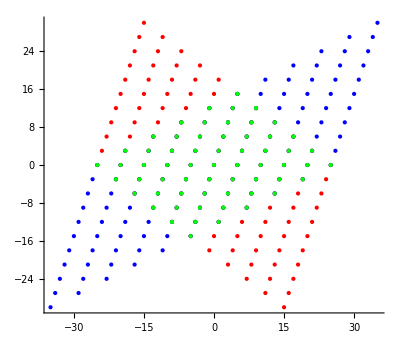

```mathematica
{a,b}=LatticeReduce[{Subscript[v, 1],Subscript[v, 2]}]
pnts2 = Table[i*a+j*b,{i,-5,5},{j,-5,5}];
Graphics[{Red,Point[Flatten[pnts2,1]],Blue,Point[Flatten[pnts,1]],Green, Point@Intersection[Flatten[pnts,1],Flatten[pnts2,1]]},Axes->True]
ClearAll[a,b]
```

{5,0}, {1,3} также базис

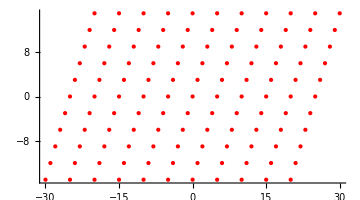

```mathematica
pnts = Table[i*{5,0}+j*{1,3},{i,-5,5},{j,-5,5}];
Graphics[{Red,Point[Flatten[pnts,1]]},Axes->True]
```

```mathematica
√Det[Outer[#1.#2&,{Subscript[v, 1],Subscript[v, 2]},{Subscript[v, 1],Subscript[v, 2]},1]]
```

15

```mathematica
Min@Table[If[#==0.,100,#]&@Norm[a*Subscript[v, 1]+b*Subscript[v, 2]//N],{a,-50,50},{b,-50,50}]
```

3.16228

```mathematica
%^2
```

10.

{1, 3}

```mathematica
Outer[#1.#2&,{Subscript[v, 1],Subscript[v, 2]},{Subscript[v, 1],Subscript[v, 2]},1]
```

{{45,15},{15,10}}

### Задание 2.

Написать функцию, которая проверяет, являются ли векторы  u_1,u_2,...,u_m∈ℝ^n базисом решетки L(v_1,v_2,...,v_m). Проверить, действительно ли найденный в Задании 1 базис является базисом решетки.

```mathematica
isBasisQ[vs_,us_]:=Abs@Det[us.Inverse[vs]]==1
```

```mathematica
isBasisQ[{Subscript[v, 1],Subscript[v, 2]},LatticeReduce[{Subscript[v, 1],Subscript[v, 2]}]]
isBasisQ[{Subscript[v, 1],Subscript[v, 2]},{{5,0},{1,3}}]
```

True

True

```mathematica
isBasisQ[{Subscript[v, 1],Subscript[v, 2]}, {{6,3},{-1,2}}]
```

True

## Ортогонализация Грама-Шмидта

Всякие линейно независимые векторы v_1,v_2,...,v_m∈ℝ^n образуют векторное пространство
{x_1 v_1+x_2 v_2+...+x_m v_m| x_1,x_2,...,x_m∈ℝ}. 
Наиболее удобным базисом векторного пространства является базис w_1,w_2,...,w_m, который удовлетворяет свойству
<w_i,w_j>=0 при i≠j.
Такой базис называется ортогональным.
Скалярное произведение порождает норму вектора
||w||:=√(<w,w>).
Квадрат нормы вектора  w обозначим через
 W:=<w,w>.

Процесс ортогонализации Грама-Шмидта.
Вход. Линейно независимые векторы v_1,v_2,...,v_m∈ℝ^n.
Выход. Ортогональный базис векторного пространства,  образованного базисными векторами v_1,v_2,...,v_m.
  1. Для i=1,2,3,...,m выполнить шаги 1.1–1.3.
      1.1. Присвоить w_i:=v_i.
      1.2. Для j=1,2,...,i-1 вычислить
                     μ_(i,j):=(<v_i,w_j>)/W_j,   w_i:=w_i-μ_(i,j)w_j.
      1.3. Положить μ_(i,i):=1, W_i:=<w_i,w_i>.
   2. Выдаем результат w_1,w_2,..., w_m.
   
Отметим, что кроме ортогонального базиса w_1,w_2,..., w_m алгоритм вычисляет также норму в квадрате W_i  и коэффициенты μ_(i,j), которые пригодятся нам в дальнейших алгоритмах.

### Задание 3.

Реализовать ортогонализацию Грама-Шмидта.

```mathematica
ClearAll[GramShmidt]
GramShmidt[vectors_]:=Block[{m=Length[vectors],i,j,w,Ms,Ws},w=Array[0&,m];Ms=Array[0&,{m,m}];Ws = Array[1&,m];
For[i=1,i<=m,i++,w[[i]]=vectors[[i]];
For[j=1,j<i,j++,
Ms[[i,j]]=(vectors[[i]].w[[j]])/(w[[j]].w[[j]]);w[[i]]=w[[i]]-Ms[[i,j]]*w[[j]]
];
Ms[[i,i]]=1;Ws[[i]]=w[[i]].w[[i]]];{{Ms,Ws},w}]
```

```mathematica
GramShmidt[{{4,5}, {4,2}}]
```

{{{{1,0},{26/41,1}},{41,144/41}},{{4,5},{60/41,-48/41}}}

## LLL-приведенный базис

К сожалению, для решеток ортогонального базиса как правило не существует, так как μ_(i,j) в общем случае не являются целыми.
Определение. Базис v_1,v_2,...,v_m∈ℝ^n решетки называется LLL-приведенным, если:
1. Для всех i,j,  1≤j<i≤m,  (|μ_(i,j)|≤1/2);
2. Для k=2,3,...,m  справедливо неравенство
(3/4-(μ_(k,k-1))^2)W_(k-1)≤W_k.
Здесь w_i,W_i, μ_(i,j) получены в процессе ортогонализации Грама-Шмидта.

### Задание 4.

```mathematica
isL3Q[{Ms_,Ws_}]:=Return[If[Max@Abs[Ms[[#,;;#-1]]&/@Range[Length[Ms]]]<=0.5,AllTrue[(0.75-Ms[[#,#-1]])*Ws[[#-1]]<=Ws[[#]]&/@Range[2,Length[Ms]],TrueQ],False]]
```

```mathematica
isL3Q[GramShmidt[{Subscript[v, 1],Subscript[v, 2]}][[1]]]
```

False

Написать функцию, которая проверяет, является ли базис v_1,v_2,...,v_m∈ℝ^n  LLL-приведенным.

LLL - алгоритм.
Вход. Базис  v_1,v_2,...,v_m∈ℝ^n решетки.
Выход. LLL-приведенный базис.
1. Для i=1,2,3,...,m выполнить шаги 1.1–1.3.
       1.1. Присвоить w_i:=v_i.
       1.2. Для j=1,2,...,i-1 вычислить
                     μ_(i,j):=(<v_i,w_j>)/W_j,   w_i:=w_i-μ_(i,j)w_j.
      1.3. Положить μ_(i,i):=1, W_i:=<w_i,w_i>.
2. Присвоить k:=2.
3. Если |μ_(k,k-1)|>1/2, то выполнить 3.1-3.3.
      3.1.  r:=Round[μ_(k,k-1)].
      3.2.  v_k:=v_k-r v_(k-1).
      3.3. Для j=1,2,...,k-1 положить μ_(k,j):=μ_(k,j)-r μ_(k-1,j).
4.  Если W_k<(3/4-(μ_(k,k-1))^2)W_(k-1), то выполнить 4.1-4.5.
      4.1. μ:=μ_(k,k-1), W:=W_k+μ^2 W_(k-1),
            μ_(k,k-1):=(μ W_(k-1))/W, W_k:=(W_(k-1)W_k)/W, W_(k-1):=W.
      4.2. Поменять местами v_k и v_(k-1).
      4.3. Для j=1,2,...,k-2 поменять местами μ_(k,j) и μ_(k-1,j).
      4.4. Для s:=k+1,k+2,...,m положить
            t:=μ_(s,k),  μ_(s,k):=μ_(s,k-1)-μ t, μ_(s,k-1):=t+μ_(k,k-1)μ_(s,k).
      4.5. Присвоить k:=max{2,k-1} и перейти к шагу 3.
5.  Если W_k≥(3/4-(μ_(k,k-1))^2)W_(k-1), то для i=k-2,k-3,...,1 при условии, что |μ_(k,i)|>1/2 выполнить 5.1-5.3.
      5.1.  r:=Round[μ_(k,i)].
      5.2.  v_k:=v_k-r v_i.
      5.3. Для j=1,2,...,i положить μ_(k,j):=μ_(k,j)-r μ_(i,j).
6. k:=k+1.
7.  Если k≤m, то перейти к шагу 3.
8.  Результат  v_1,v_2,...,v_m.

Литература: Маховенко, Е.Б. Теоретико-числовые методы в криптографии / Е.Б. Маховенко.  – М.: Гелиос АРВ, 2006. – 320с.

### по шагам

Рассмотрим пример работы LLL-алгоритма. Пусть

```mathematica
vv={{31,54,43},{39,72,57},{72,40,96}}
```

{{31,54,43},{39,72,57},{72,40,96}}

```mathematica
GramShmidt[v]
```

{{{{1,1,1},{3774/2863,1,1},{4260/2863,-452/27,1}},{5726,12150/2863,6400/3}},{{31,54,43},{-5337/2863,2340/2863,909/2863},{-16/3,-80/3,112/3}}}

После выполнения первого шага имеем

```mathematica
w//MatrixForm
μ//MatrixForm
W
```

(31 | 54 | 43
-5337/2863 | 2340/2863 | 909/2863
-16/3 | -80/3 | 112/3)

(1 | 0 | 0
3774/2863 | 1 | 0
4260/2863 | -452/27 | 1)

{5726,12150/2863,6400/3}

После 3 шага

```mathematica
k
μ//MatrixForm
W
v
```

2

(1 | 0 | 0
911/2863 | 1 | 0
4260/2863 | -452/27 | 1)

{5726,12150/2863,6400/3}

{{31,54,43},{8,18,14},{72,40,96}}

После 4 шага

```mathematica
k
μ//MatrixForm
W
v
```

2

(1 | 0 | 0
911/292 | 1 | 0
330/73 | 184/27 | 1)

{584,6075/146,6400/3}

{{8,18,14},{31,54,43},{72,40,96}}

Условие W_k≥(3/4-(μ_(k,k-1))^2)W_(k-1) LLL-приведенного базиса не выполнилось, поэтому пришлось менять местами векторы v_1 и v_2. Возвращаемся к третьему шагу.

Выполнив третий и четвертый шаг, получим

```mathematica
k
μ//MatrixForm
W
v
```

2

(1 | 0 | 0
7/5 | 1 | 0
12 | 100/27 | 1)

{50,486,6400/3}

{{7,0,1},{8,18,14},{72,40,96}}

Снова выполним третий шаг

```mathematica
k
μ//MatrixForm
W
v
```

2

(1 | 0 | 0
2/5 | 1 | 0
12 | 100/27 | 1)

{50,486,6400/3}

{{7,0,1},{1,18,13},{72,40,96}}

Теперь условие

```mathematica
W⟦k⟧<(3/4-μ⟦k,k-1⟧^2)W⟦k-1⟧
```

False

Наконец-то, переходим к шагу 5

```mathematica
k
μ//MatrixForm
W
v
```

3

(1 | 0 | 0
2/5 | 1 | 0
12 | 100/27 | 1)

{50,486,6400/3}

{{7,0,1},{1,18,13},{72,40,96}}

k = 3 ≤ m = 3, поэтому еще раз выполним шаги 3 – 5

```mathematica
k
μ//MatrixForm
W
v
```

4

(1 | 0 | 0
2/5 | 1 | 0
2/5 | -8/27 | 1)

{50,486,6400/3}

{{7,0,1},{1,18,13},{-2,-32,34}}

k>m, поэтому выдаем ответ

```mathematica
v
```

{{7,0,1},{1,18,13},{-2,-32,34}}

Проверим результат встроенной функцией

```mathematica
LatticeReduce[{{31,54,43},{39,72,57},{72,40,96}}]
```

{{7,0,1},{1,18,13},{-2,-32,34}}

### Задание 5.

```mathematica
LLLAlg[vectors_]:=Block[{Ms,Ws,w,v=vectors,m=Length[vectors],r,tmpm,tmpW,tmp,t,k,j,i,s},
{{Ms,Ws},w}=GramShmidt[vectors];
For[k=2,k<=m,k++,Print["Before 3"];
If[Abs[Ms[[k,k-1]]]>0.5,
r=Round[Ms[[k,k-1]]];
v[[k]]=v[[k]]-r*v[[k-1]];
For[j=1,j<=k-1,j++,Ms[[k,j]]=Ms[[k,j]]-r*Ms[[k-1,j]]]];
Print["Before 4"];
If[Ws[[k]]<Ws[[k-1]]*(0.75-Ms[[k,k-1]]^2),
tmpm=Ms[[k,k-1]];
tmpW=Ws[[k]]+tmpm^2*Ws[[k-1]];
Ms[[k,k-1]]=(tmpm*Ws[[k-1]])/tmpW;
Ws[[k]]=(Ws[[k-1]]*Ws[[k]])/tmpW;Ws[[k-1]]=tmpW;
tmp=v[[k]];v[[k]]=v[[k-1]];v[[k-1]]=tmp;
For[j=1,j<=k-2,j++,
tmp=Ms[[k,j]];Ms[[k,j]]=Ms[[k-1,j]];Ms[[k-1,j]]=tmp];
For[s=k+1,s<=m,s++,
t=Ms[[s,k]];
Ms[[s,k]]=Ms[[s,k-1]]-t*tmpm;
Ms[[s,k-1]]=t+Ms[[k,k-1]]*Ms[[s,k]]
];
k=Max[2,k-1]-1;Continue[]];
Print["Before 5"];
If[Ws[[k]]>=(0.75-Ms[[k,k-1]]^2)*Ws[[k-1]],
For[i=k-2,i>=1,i--,
If[Abs[Ms[[k,i]]]>0.5,
r=Round[Ms[[k,i]]];
v[[k]]=v[[k]]-r*v[[i]];
For[j=1,j<=i,j++,Ms[[k,j]]=Ms[[k,j]]-r*Ms[[i,j]]]
]
]
]
];
v]
```

```mathematica
LLLAlg[{Subscript[v, 1],Subscript[v, 2]}]
```

Before 3

Before 4

Before 3

Before 4

Before 5

{{1,3},{4,-3}}

```mathematica
LatticeReduce[{Subscript[v, 1],Subscript[v, 2]}]
```

{{1,3},{4,-3}}

```mathematica
vv={{31,54,43},{39,72,57},{72,40,96}};
```

```mathematica
AbsoluteTiming[LLLAlg[vv]]
AbsoluteTiming[LatticeReduce[vv]]
```

Before 3

Before 4

Before 3

Before 4

Before 3

Before 4

Before 5

Before 3

Before 4

Before 5

{0.0006553,{{7,0,1},{1,18,13},{-2,-32,34}}}

{0.0001411,{{7,0,1},{1,18,13},{-2,-32,34}}}

Реализовать LLL-алгоритм. Сравнить результаты и время вычислений со встроенной функцией LatticeReduce.

До десятой версии Mathematica работала согласно вышеописанному алгоритму

```mathematica
LatticeReduce[{{6,3},{1,3}}]
```

{{1,3},{4,-3}}

А в десятой и выше по другому:

```mathematica
LatticeReduce[{{6,3},{1,3}}]
```

{{1,3},{5,0}}

### Задание 6.

Найти алгоритм, по которому работает функция LatticeReduce в пакете Mathematica версии 10 и выше. За решение данной задачи на экзамене 10 первому решившему.

```mathematica
Findpi2[b_,bs_]:=Return[#.#&@(Inverse[Outer[#1.#2&,bs,bs,1]].b)]
```

```mathematica
Findpi2[{1,1},{Subscript[v, 1],Subscript[v, 2]}]
```

37/2025

```mathematica
LLLAlg2[vectors_,delta_:0.75]:=Block[{v=vectors,n=Length[vectors],i,j,Ms,Ws,w,tmp},
{{Ms,Ws},w}=GramShmidt[v];
While[True,
For[i=1,i<n,i++,
For[j=i-1,j>=1,j--,
v[[i]]=v[[i]]-Round[Ms[[i,j]]]*v[[j]]
];
];
For[i=1,i<=n,i++,
If[delta*Findpi2[v[[i]],v]>Findpi2[v[[i+1]],v],
tmp = v[[i]];
v[[i]] = v[[i-1]];
v[[i-1]] = tmp;Break[],Return[v]]]];
v]
```

```mathematica
LLLAlg2[{Subscript[v, 1],Subscript[v, 2]}]
```

{{6,3},{1,3}}

### Задание 7.

Может ли существовать другой LLL-приведенный базис решетки, отличный от того, который выдает LLL-алгоритм?

LLL-приведенный базис обладает свойствами

1) ||v_i(||)^2≤2^(j-1)||w_j(||)^2  для всех 1≤i≤j≤m. 
2) ||v_i(||)^2≤(2^(j-2)+2^(j-i-1))||w_j(||)^2  для всех 1≤i≤j≤m.

### Задание 8.

Существует ли решетка, для которой для некоторых i, j (1≤i<j≤m) справедливо равенство

||v_i(||)^2=2^(j-1)||w_j(||)^2.

```mathematica
vv1 = {{1,0},{0,1}}
Norm[vv1[[2]]]^2==2^(1-1)*Norm[vv1[[1]]]^2
```

{{1,0},{0,1}}

True

### Задание 9.

Существует ли решетка, для которой для некоторых i, j (1≤i<j≤m) справедливо равенство

||v_i(||)^2=(2^(j-2)+2^(j-i-1))||w_j(||)^2.

```mathematica
vv2 = {{2,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
i=1;
j=3;
Norm[vv2[[i]]]^2==(2^(j-2)+2^(j-i-1))*Norm[vv2[[j]]]^2
```

{{2,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

True